### GHZ State

#### GHZ State Measurement

Start with a GHZ state,

GHZ=1/(√2)(000…+111…),

sequentially measure each single qubit, in either X,Y,Z basis.

Measurement may cause the state to collapse or change the relative phase between 000… and 111…. In general, the intermediate state during the measurement process takes the form of

ψ=α000…+β111…,

which can be denoted by a two component state vector (α,β)ᵀ.

Take 000… and 111… as our basis, ψ is represented as

ψ=(α
β),

The initial condition is α=β=1/(√2).

Normalization is always assumed (|α|)^2+(|β|)^2=1.

Measuring the first qubit

If X_1 is measured,

p(X_1=±1)=Piecewise[{{1/2, if it is not the last qubit}, {1/2(|α±β|)^2, if it is the last qubit}}]

If X_1=±1 is observed, the state collapses to

α000…+β111…→^(X_1=±1)α X_1=±1X_1=±100…+β X_1=±1X_1=±111…
=X_1=±1(α00…±β11…),

which corresponds to

(α
β)→^(X_1=±1)(α
±β).

If Y_1 is measured,

p(Y_1=±1)=Piecewise[{{1/2, if it is not the last qubit}, {1/2(|α∓ⅈ β|)^2, if it is the last qubit}}]

If Y_1=±1 is observed, the state collapses to

α000…+β111…→^(Y_1=±1)α Y_1=±1Y_1=±100…+β Y_1=±1Y_1=±111…
=Y_1=±1(α00…∓ⅈ β11…),

which corresponds to

(α
β)→^(Y_1=±1)(α
∓ⅈ β).

If Z_1 is measured,

p(Z_1=±1)=(1±((|α|)^2-(|β|)^2))/2.

If Z_1=±1 is observed, the state collapses to

α000…+β111…→^(Z_1=+1)Z_1=+100…,
α000…+β111…→^(Z_1=-1)Z_1=-100…,

which corresponds to

(α
β)→^(Z_1=+1)(1
0),
(α
β)→^(Z_1=-1)(0
1).

```mathematica
GHZMeasure[qubits_,samples_]:=Block[{measure},
measure[state_,"X"]:=Block[{α,β,ps,sgn},
{α,β}=state["ψ"];
ps=If[state["n"]==1,Abs[α+{1,-1}β]^2/2,{1,1}/2];
sgn=RandomChoice[ps->{1,-1}];
{<|1->"X+",-1->"X-"|>[sgn],
<|"ψ"->{α,sgn β},"n"->state["n"]-1|>}];
measure[state_,"Y"]:=Block[{α,β,ps,sgn},
{α,β}=state["ψ"];
ps=If[state["n"]==1,Abs[α-ⅈ{1,-1}β]^2/2,{1,1}/2];
sgn=RandomChoice[ps->{1,-1}];
{<|1->"Y+",-1->"Y-"|>[sgn],
<|"ψ"->{α,-ⅈ sgn β},"n"->state["n"]-1|>}];
measure[state_,"Z"]:=Block[{α,β,ps,sgn},
{α,β}=state["ψ"];
ps=(1+{1,-1}(Abs[α]^2-Abs[β]^2))/2;
sgn=RandomChoice[ps->{1,-1}];
{<|1->"Z+",-1->"Z-"|>[sgn],
<|"ψ"->{1+sgn,1-sgn}/2,"n"->state["n"]-1|>}];
Table[FoldPairList[measure,
<|"ψ"->{1,1}/Sqrt[2],"n"->qubits|>,
RandomChoice[{"X","Y","Z"},qubits]],samples]];
```

Generate 100 repeated measurements on 2-qubit GHZ state.

```mathematica
Sort@GHZMeasure[2,100]
```

{{X-,X-},{X-,X-},{X-,X-},{X-,X-},{X-,X-},{X-,X-},{X-,Y-},{X-,Y+},{X-,Y+},{X-,Y+},{X-,Z-},{X-,Z-},{X-,Z-},{X-,Z-},{X-,Z+},{X-,Z+},{X-,Z+},{X-,Z+},{X+,X+},{X+,X+},{X+,X+},{X+,Y-},{X+,Y-},{X+,Y-},{X+,Y+},{X+,Y+},{X+,Y+},{X+,Z-},{X+,Z-},{X+,Z-},{X+,Z+},{X+,Z+},{X+,Z+},{X+,Z+},{Y-,X-},{Y-,X-},{Y-,X+},{Y-,X+},{Y-,X+},{Y-,Y+},{Y-,Y+},{Y-,Y+},{Y-,Z-},{Y-,Z-},{Y-,Z-},{Y-,Z-},{Y-,Z-},{Y-,Z-},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y-,Z+},{Y+,X-},{Y+,X+},{Y+,X+},{Y+,X+},{Y+,Y-},{Y+,Y-},{Y+,Y-},{Y+,Y-},{Y+,Z-},{Y+,Z+},{Y+,Z+},{Z-,X-},{Z-,X-},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,X+},{Z-,Y-},{Z-,Y-},{Z-,Y-},{Z-,Y-},{Z-,Y+},{Z-,Y+},{Z-,Y+},{Z-,Y+},{Z-,Z-},{Z-,Z-},{Z-,Z-},{Z-,Z-},{Z-,Z-},{Z+,X+},{Z+,Y-},{Z+,Y+},{Z+,Y+},{Z+,Z+},{Z+,Z+},{Z+,Z+},{Z+,Z+},{Z+,Z+},{Z+,Z+}}

```mathematica
SeedRandom[0];
Row[Table[Grid[MapIndexed[Block[{op,s,i,col},
op=StringTake[#1,{1}];
s=StringTake[#1,{2}];
i=Last@#2;
col=<|"X"->Red,"Y"->Green,"Z"->Blue|>[op];
Graphics[{{{<|"+"->Lighter[col,0.9],"-"->Lighter[col,0.2]|>[s],Rectangle[{0,-0.5},{1,0},RoundingRadius->0.2],Rectangle[{0,-0.2},{1,0}]},{col,AbsoluteThickness[2],Line[{{0,0},{1,0}}]},{EdgeForm[Directive[col,AbsoluteThickness[2]]],Opacity[0],Rectangle[{0,-0.5},{1,1},RoundingRadius->0.2]}},{col,Text[StringTemplate["\!\(`1`\_`2`\)"][op,i],{0.5,0.45}]},{<|"+"->Black,"-"->White|>[s],Text[Style[s,FontFamily->"Helvetica",Bold],{0.5,-0.25}]}},PlotRangePadding->None,ImageSize->22]]&,GHZMeasure[4,4],{2}],Spacings->{-0,1}],5],Spacer[1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Row/@MapIndexed[Block[{op,s,i,col},
op=StringTake[#1,{1}];
s=StringTake[#1,{2}];
i=Last@#2;
col=<|"X"->Red,"Y"->Green,"Z"->Blue|>[op];
Graphics[{{{<|"+"->Lighter[col,0.9],"-"->Lighter[col,0.2],"?"->Lighter[col,0.75]|>[s],Rectangle[{0,-0.5},{1,0},RoundingRadius->0.2],Rectangle[{0,-0.2},{1,0}]},{If[s=="?",Lighter[col,0.5],col],AbsoluteThickness[2],Line[{{0,0},{1,0}}]},{EdgeForm[Directive[If[s=="?",Lighter[col,0.5],col],AbsoluteThickness[2]]],Opacity[0],Rectangle[{0,-0.5},{1,1},RoundingRadius->0.2]}},{If[s=="?",Lighter[col,0.5],col],Text[StringTemplate["\!\(`1`\_`2`\)"][op,i],{0.5,0.45}]},If[s!="?",{<|"+"->Black,"-"->White|>[s],Text[Style[s,FontFamily->"Helvetica",Bold],{0.5,-0.25}]}]},PlotRangePadding->None,ImageSize->22]]&,{{"Z+","Z+","Y+","X-"},{"Z+","Z+","Y+","X+"},{"Z+","Z+","Y?","X?"},{"Z?","Z?","Y?","X?"}},{2}]
```

```mathematica
{-Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics-}
```

#### Probability Evaluation

Given a sequence of single-qubit measurement outcomes on the GHZ state, the probability for this sequence to appear can be evaluated by

p(x)=(|(⊗_i x_i)GHZ|)^2
=1/2(|(⊗_i x_i)000…+(⊗_i x_i)111…|)^2
=1/2(|∏_i x_i0+∏_i x_i1|)^2,

where

X_i=±10=1/(√2),X_i=±11=(±1)/(√2),
Y_i=±10=1/(√2),Y_i=±11=(∓ⅈ)/(√2),
Z_i=±10=(1±1)/2,X_i=±11=(1∓1)/(√2).

```mathematica
GHZProb[sequence_]:=Abs[Total[Times@@(
<|"X+"->{1,1}/Sqrt[2],"X-"->{1,-1}/Sqrt[2],
"Y+"->{1,-ⅈ}/Sqrt[2],"Y-"->{1,ⅈ}/Sqrt[2],
"Z+"->{1,0},"Z-"->{0,1}|>/@sequence)]]^2/2
```

```mathematica
#->GHZProb[#]&/@GHZMeasure[5,10]
```

{{X-,X+,X-,Z-,X-}→1/32,{X-,Y-,Z-,Y+,X+}→1/32,{X-,Z-,Y+,Y-,Y-}→1/32,{X+,Y-,Z-,Z-,Y+}→1/16,{Y-,Z-,Z-,Y+,X-}→1/16,{Y+,X+,Y-,Y-,Y+}→1/16,{Y+,X+,Y+,Z+,Y+}→1/32,{Z-,Y-,X-,Y+,X-}→1/32,{Z+,X+,X+,X+,Z+}→1/16,{Z+,X+,Y+,Z+,X+}→1/16}

```mathematica
GHZProb[{"Z+","Z+","Z+","Z+","Z+"}]
```

1/2

```mathematica
GHZProb[{"X+","X+","X+","X+","X+"}]
```

1/16

#### Classical Shadow Reconstruction

The original density matrix can be reconstructed by

ρ=𝔼(⊗_i(3x_ix_i-𝟙))
=𝔼(⊗_i(𝟙+3O[x_i])/2).

```mathematica
Shadow[sequence_]:=Block[{Os,kron},
Os=<|"X+"->PauliMatrix[1],"X-"->-PauliMatrix[1],
"Y+"->PauliMatrix[2],"Y-"->-PauliMatrix[2],
"Z+"->PauliMatrix[3],"Z-"->-PauliMatrix[3]|>/@sequence;
kron[A_]:=A;
kron[As__]:=KroneckerProduct[As];
kron@@((IdentityMatrix[2]+3#)/2&/@Os)]
```

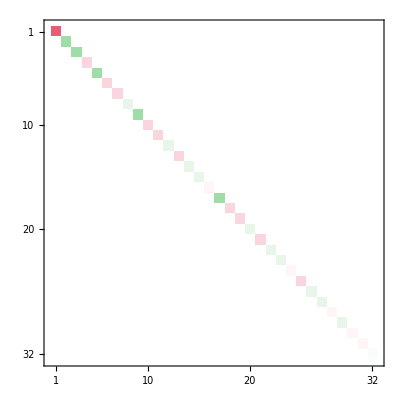

```mathematica
Shadow[{"Z+","Z+","Z+","Z+","Z+"}]//ComplexMatrixPlot
```

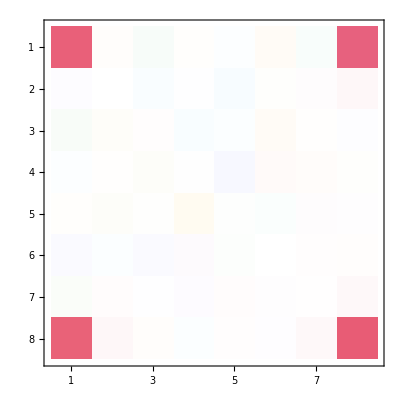

```mathematica
Mean[N/@Shadow/@GHZMeasure[3,10000]]//ComplexMatrixPlot
```

##### Data Selection

```mathematica
Length@Cases[GHZMeasure[3,30000],s_/;FreeQ[s,"Z+"|"Z-"]]
```

8975

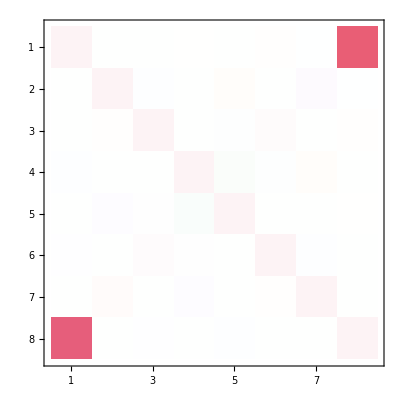

```mathematica
Mean[N/@Shadow/@Cases[GHZMeasure[3,10000],s_/;FreeQ[s,"Z+"|"Z-"]]]//ComplexMatrixPlot
```

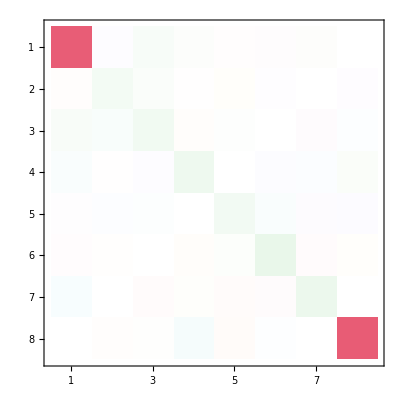

```mathematica
Mean[N/@Shadow/@DeleteCases[GHZMeasure[3,10000],s_/;FreeQ[s,"Z+"|"Z-"]]]//ComplexMatrixPlot
```

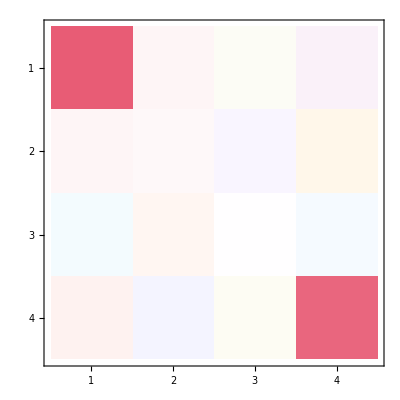

```mathematica
Mean[N/@Shadow/@GHZMeasure[3,1000]⟦All,;;-2⟧]//ComplexMatrixPlot
```

### Holographic Generative Model

#### Generative Map

Consider a set of ℤ_2×ℤ_4 hidden variables in the holographic bulk, each of the form (a_i,b_i). The generative map is given by

G[(a_1,b_1),(a_2,b_2)]=[(a_1,b_1+_ℤ_4 b_2),(a_1,b_1-_ℤ_4 b_2)].

In the last layer, query observable Z with 1/3 probability and X∨Y with 2/3 probability.

If Z_i is queried, return a_i as outcome.

a_i |  
0 | Z+
1 | Z-

If X_i∨Y_i is queried, return b_i as outcome.

b_i |  
0 | X+
1 | Y+
2 | X-
3 | Y-

```mathematica
HolographicGenerator[layers_,samples_]:=
Block[{gmap,glayer,translator,sample},
gmap[{{a1_,b1_},{a2_,b2_}}]:=
{{a1,Mod[b1+b2,4]},{a1,Mod[b1-b2,4]}};
glayer[hs_]:=Block[{n=Length@hs},
Flatten[gmap/@Thread@{hs,
Thread@{RandomInteger[{0,1},n],RandomInteger[{0,3},n]}},1]];
sample:=Nest[glayer,{{RandomInteger[{0,1}],0}},layers];
translator["Z",{a_,b_}]:=<|0->"Z+",1->"Z-"|>[a];
translator["XY",{a_,b_}]:=<|0->"X+",1->"Y+",2->"X-",3->"Y-"|>[RandomInteger[{0,3}]];
Table[translator@@@Thread@{RandomChoice[{1/3,2/3}->{"Z","XY"},
2^layers],sample},samples]];
```

```mathematica
HolographicGenerator[layers_,samples_]:=
Block[{gmap,glayer,translator,sample},
gmap[{{a1_,b1_},{a2_,b2_}}]:=
{{a1,Mod[b1+b2,4]},{a1,Mod[b1-b2,4]}};
glayer[hs_]:=Block[{n=Length@hs},
Flatten[gmap/@Thread@{hs,
Thread@{RandomInteger[{0,1},n],RandomInteger[{0,3},n]}},1]];
sample:=Nest[glayer,{{RandomInteger[{0,1}],0}},layers];
translator["Z",{a_,b_}]:=<|0->"Z+",1->"Z-"|>[a];
translator["XY",{a_,b_}]:=<|0->"X+",1->"Y+",2->"X-",3->"Y-"|>[b];
Table[translator@@@Thread@{RandomChoice[{1/3,2/3}->{"Z","XY"},
2^layers],sample},samples]];
```

```mathematica
GHZMeasure[4,10]
```

{{Z-,X+,X+,Y+},{X-,Y-,X-,X-},{Z-,Z-,Z-,Z-},{Y+,Y-,X-,Y-},{X+,X-,X+,Z+},{X-,Z+,X+,Y-},{X-,X+,Y+,X-},{Z-,Y+,Z-,Z-},{Y-,Y-,Y-,Y-},{X-,X+,X-,X+}}

```mathematica
HolographicGenerator[2,10]
```

{{Y-,Y-,X-,X+},{Y-,Y-,Z+,X-},{Y+,Z-,Y-,Y-},{X+,X-,Y+,Y+},{X-,Z-,Y+,Y+},{X-,X-,X+,Z+},{X+,Z-,Z-,Y+},{X-,Z+,Y+,Y-},{Z+,Z+,Y-,Y+},{Z-,X+,Y+,Z-}}

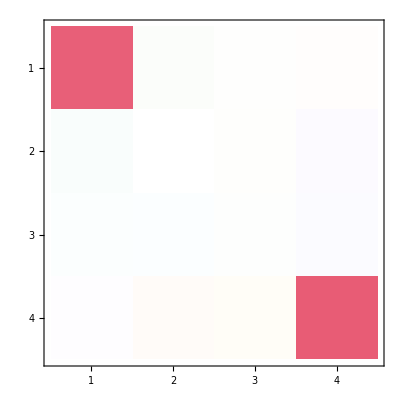

```mathematica
Mean[N/@Shadow/@HolographicGenerator[1,10000]]//ComplexMatrixPlot
```